```mathematica
alpmd[ai_]:=0.0003*ai^3-0.036*ai^2+1.5206*ai+20;
alpmu[ai_]:=-0.00042*ai^3+0.0236*ai^2+0.129*ai+20;
aind[alpm_]:=Sqrt[Cos[alpm]/(1-Cos[alpm])];
norm[a_]:=Beta[1/a+1,a+1];
```

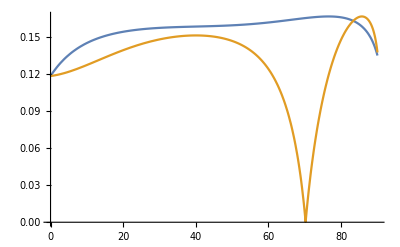

```mathematica
Plot[{norm[aind[alpmd[ai]*Pi/180]],norm[aind[alpmu[ai]*Pi/180]]},{ai,0,90},PlotRange->All]
```

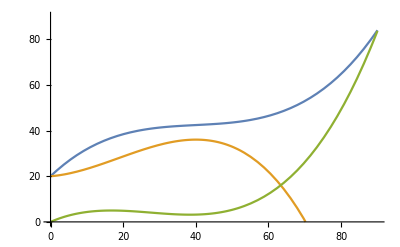

```mathematica
Plot[{alpmd[ai],alpmu[ai],(alpmd[ai]-alpmu[ai])/2},{ai,0,90},PlotRange->{0,90}]
```

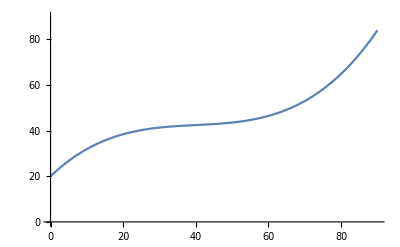

```mathematica
Plot[alpmd[ai],{ai,0,90},PlotRange->{0,90}]
```

```mathematica
alpmd[90]
```

83.954

```mathematica
Solve[a^2==Cos[al]/(1-Cos[al]),al]
```

{{al→ConditionalExpression[-ArcCos[a^2/(1+a^2)]+2 π C[1], C[1]∈ℤ]},{al→ConditionalExpression[ArcCos[a^2/(1+a^2)]+2 π C[1], C[1]∈ℤ]}}

```mathematica
Integrate[(1+Cos[(x-m)/s*Pi]),{x,m-s,Y}]
```

-m+s+Y-(s Sin[(π (m-Y))/s])/π

```mathematica
-m+s+Y-(s Sin[(π (A+B*phi-Y))/s])/π
```

```mathematica
Integrate[(1+a*Cos[phi])/(-m+s+Y-(s Sin[(π (A+B*phi-Y))/s])/π),{phi,0,Pi}]
```

$Aborted

```mathematica
Simplify[Integrate[(1+Cos[(x-m)/s*Pi]),{x,m-s,m+s}]]
```

2 s

```mathematica
FullSimplify[Integrate[Integrate[(1+A*Cos[phi])*(1+Cos[x-(a+b*phi)*Pi/s]),{phi,0,2*Pi}],{x,m-s,m+s}]]
```

4 π s+(4 s ((1+A) b^2 π^2-s^2) Cos[m-(π (a+b π))/s] Sin[(b π^2)/s] Sin[s])/(b π (b π-s) (b π+s))

```mathematica
Integrate[Integrate[(1+A*Cos[phi])*(1+Cos[x-(a+b*phi)*Pi/s]),{phi,phi0,phi1}],{x,m-s,m+s}]+Integrate[Integrate[(1+A*Cos[phi])*(1+Cos[x-(a+b*phi)*Pi/s]),{phi,0,phi0}],{x,0,m+s}]+Integrate[Integrate[(1+A*Cos[phi])*(1+Cos[x-(a+b*phi)*Pi/s]),{phi,phi1,2*Pi}],{x,0,m+s}]
```

m phi0-m phi1+2 m π+phi0 s-phi1 s+2 π s+(s (Cos[((a+b phi1) π)/s]-Cos[m-((a+b phi1) π)/s+s]))/(b π)+(s (-Cos[(π (a+2 b π))/s]+Cos[m-(π (a+2 b π))/s+s]))/(b π)-(A b π s (-Cos[(π (a+2 b π))/s]+Cos[m-(π (a+2 b π))/s+s]))/((-b π+s) (b π+s))+A m Sin[phi0]+A s Sin[phi0]-A m Sin[phi1]-A s Sin[phi1]+(4 s Cos[(-2 a π-b phi0 π+s (m+s))/(2 s)] Sin[(b phi0 π)/(2 s)] Sin[(m+s)/2])/(b π)+s (-2 phi0+2 phi1-2 A Sin[phi0]+2 A Sin[phi1]+(2 (Sin[m-((a+b phi0) π)/s]-Sin[m-((a+b phi1) π)/s]) Sin[s])/(b π)+(A Sin[s] (-(b π+s) Sin[m+phi0-((a+b phi0) π)/s]+(b π+s) Sin[m+phi1-((a+b phi1) π)/s]+(b π-s) (Sin[(a π+b phi0 π-m s+phi0 s)/s]-Sin[(a π+b phi1 π-m s+phi1 s)/s])))/((-b π+s) (b π+s)))+(A s (2 b π (-Cos[(a π)/s]+Cos[m-(a π)/s+s])+(-b π+s) (-Cos[phi0+((a+b phi0) π)/s]+Cos[(a π+b phi0 π+phi0 s-s (m+s))/s])+2 (b π+s) Sin[(m+s)/2] Sin[(-2 a π-2 b phi0 π+s (m+2 phi0+s))/(2 s)]))/(2 (-b π+s) (b π+s))+(A b π s Sin[(m+s)/2] Sin[(-2 a π-2 b phi1 π+s (m-2 phi1+s))/(2 s)])/((b π-s) (b π+s))+(A s^2 Sin[(m+s)/2] Sin[(-2 a π-2 b phi1 π+s (m-2 phi1+s))/(2 s)])/((-b π+s) (b π+s))+(A b π s Sin[(m+s)/2] Sin[(-2 a π-2 b phi1 π+s (m+2 phi1+s))/(2 s)])/((b π-s) (b π+s))-(A s^2 Sin[(m+s)/2] Sin[(-2 a π-2 b phi1 π+s (m+2 phi1+s))/(2 s)])/((-b π+s) (b π+s))

```mathematica
FullSimplify[%32]
```

m phi0-m phi1+2 m π-phi0 s+phi1 s+2 π s+(A b π s (Cos[(a π)/s]-Cos[m-(a π)/s+s]))/(b^2 π^2-s^2)+(s (Cos[((a+b phi1) π)/s]-Cos[m-((a+b phi1) π)/s+s]))/(b π)+(s (-Cos[(π (a+2 b π))/s]+Cos[m-(π (a+2 b π))/s+s]))/(b π)+(A b π s (-Cos[(π (a+2 b π))/s]+Cos[m-(π (a+2 b π))/s+s]))/(b^2 π^2-s^2)+(A s (-Cos[phi0+((a+b phi0) π)/s]+Cos[(a π+b phi0 π+phi0 s-s (m+s))/s]))/(2 (b π+s))+A m Sin[phi0]-A s Sin[phi0]-A m Sin[phi1]+A s Sin[phi1]+(2 s (Sin[m-((a+b phi0) π)/s]-Sin[m-((a+b phi1) π)/s]) Sin[s])/(b π)+(4 s Cos[(-2 a π-b phi0 π+s (m+s))/(2 s)] Sin[(b phi0 π)/(2 s)] Sin[(m+s)/2])/(b π)+(A s Sin[s] (-(b π+s) Sin[m+phi0-((a+b phi0) π)/s]+(b π+s) Sin[m+phi1-((a+b phi1) π)/s]+(b π-s) (Sin[(a π+b phi0 π-m s+phi0 s)/s]-Sin[(a π+b phi1 π-m s+phi1 s)/s])))/((-b π+s) (b π+s))+(A s Sin[(m+s)/2] Sin[(-2 a π-2 b phi0 π+s (m+2 phi0+s))/(2 s)])/(-b π+s)+(A b π s Sin[(m+s)/2] Sin[(-2 a π-2 b phi1 π+s (m-2 phi1+s))/(2 s)])/((b π-s) (b π+s))+(A s^2 Sin[(m+s)/2] Sin[(-2 a π-2 b phi1 π+s (m-2 phi1+s))/(2 s)])/((-b π+s) (b π+s))+(A b π s Sin[(m+s)/2] Sin[(-2 a π-2 b phi1 π+s (m+2 phi1+s))/(2 s)])/((b π-s) (b π+s))-(A s^2 Sin[(m+s)/2] Sin[(-2 a π-2 b phi1 π+s (m+2 phi1+s))/(2 s)])/((-b π+s) (b π+s))